```mathematica
Bernstein[n_,F_]:= ∑_(k=0)^n Binomial[n,k] x^k(1-x)^(n-k)F[k/n];
```

```mathematica
F[x_] := ⅇ^x;
```

```mathematica
G[x_]= Simplify[Bernstein[20,F]];
```

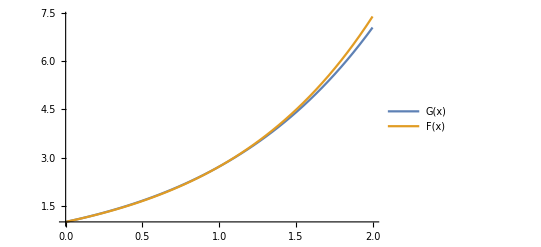

```mathematica
Plot[{G[x],F[x]},{x,0,2},PlotLegends->"Expressions"]
```

Vamos a calcular el error de aproximar la función en 2 puntos

```mathematica
N[Abs[F[2]-G[2]]]
```

2.11081

```mathematica
N[Abs[F[0.5]-G[0.5]]]
```

0.10521

Calcular el error de aproximar la función con Bernstein con 21 puntos

```mathematica
N[Abs[F[2]-G[2]]]
```

0.343677

```mathematica
N[Abs[F[0.5]-G[0.5]]]
```

0.0103357

Conclusión: A mayor puntos, mayor presición.